# Anomaly Detection su logs con il Linguaggio Wolfram

## Il linguaggio

Il Linguaggio Wolfram è un linguaggio di calcolo computazionale sviluppato da Wolfram Research. Basato sul computing, permette di eseguire complessi calcoli e di creare modelli e simulazioni in modo molto più semplice rispetto ai tradizionali linguaggi di programmazione. Grazie a un’ampia libreria di funzioni integrate, il Linguaggio Wolfram consente di esplorare e risolvere in modo interattivo problemi in svariati campi, dalla statistica alla fisica, dall’ingegneria alla finanza.

Il linguaggio ha una sintassi molto compatta, e incorpora naturalmente oggetti matematici quali numeri, elenchi, matrici, grafici e geometrie.Le capacità di visualizzazione del Linguaggio Wolfram permettono di esplorare in modo immediato i risultati dei calcoli effettuati. Il Linguaggio Wolfram è un ambiente di calcolo adatto sia a utenti esperti che a principianti. Gli utenti esperti possono sfruttarne tutta la potenza attraverso la programmazione, mentre i principianti hanno a disposizione un’interfaccia intuitiva per iniziare subito a fare scienza in modo interattivo.

Il Linguaggio Wolfram viene utilizzato in molti campi, tra cui ricerca, istruzione, finanza ed ingegneria. La sua flessibilità e completezza lo rendono uno strumento ideale per l’espressione e il controllo dei calcoli computazionali. Grazie al Linguaggio Wolfram è possibile concentrare lo sforzo cognitivo sull’intuizione e l’approfondimento dei problemi piuttosto che sullo strumento utilizzato per risolverli.

## L’approccio

Per approcciare il nostro problema, utilizziamo tecniche di apprendimento automatico non supervisionato come l’apprendimento auto-supervisionato.

In particolare, si può adottare un approccio basato su BERT (Bidirectional Encoder Representations from Transformers), una rete neurale autoregressiva in grado di catturare relazioni semantiche in grandi quantità di dati non necessariamente strutturati.

Dopo aver addestrato un modello BERT su una grande quantità di log “normali”, è possibile utilizzare lo stesso modello per generare embedding per nuovi log in ingresso, potendoli poi comparare con quelle in memoria.

## BERT

BERT è un transformer encoder-only capace di computare embedding di parole contestuali da frasi. È principalmente costituito da una serie di transformer block in sequenza.

-Graphics-

Ogni transformer layer ha due substrati: un feed-forward neural network (FFNN) e una multi-headed self-attention (MHSA). Il MHSA sublayer utilizza scaled dot-product attention per generare rappresentazioni contestuali delle parole.

Gli iniziali embedding dei token e posizionali vengono inseriti in BERT e quindi elaborati attraverso gli strati dell’encoder. I token embedding provengono da una matrice di embedding condivisa.

La capacità di BERT di elaborare l’attenzione bidirezionale sull’intera sequenza di input è ciò che gli consente di generare una profonda comprensione del contesto e produrre una rappresentazione vettoriale esaustiva per ogni parola nell’input. Questi vettori di rappresentazione possono quindi essere utilizzati per un’ampia gamma di attività di comprensione del linguaggio naturale, nel nostro caso, l’analisi dei logs.

## L’implementazione

Carichiamo i dati e raggruppiamoli in chunks.

```mathematica
chunkSize=2;
```

```mathematica
logs=(StringRiffle[#,"\n"])&/@Partition[StringSplit[Import["/home/user/Desktop/logad/HDFS_2k.log","Text"],"\n"],UpTo[chunkSize]];
```

```mathematica
Length[logs]
```

1000

```mathematica
First[logs]
```

081109 203615 148 INFO dfs.DataNode$PacketResponder: PacketResponder 1 for block blk_38865049064139660 terminating
081109 203807 222 INFO dfs.DataNode$PacketResponder: PacketResponder 0 for block blk_-6952295868487656571 terminating

```mathematica
baseModel={"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling","Size"->"117M"};
```

Definiamo il tokenizzatore, che farà da intermediario tra il testo e gli embedding.

```mathematica
tokenizer=NetExtract[NetModel[baseModel],"Input"]
```

NetEncoder[<>]

```mathematica
detokenizer=NetExtract[NetModel[baseModel],"Output"]
```

NetDecoder[<>]

Definiamo alcuni iperparametri.

```mathematica
device="GPU";
```

```mathematica
tokensDimLM=50257+1;
predictorDropoutRate=0.2;
sequenceLength=512;
hiddenDim=128;
headsDim=16;
```

Definiamo l’encoding posizionale.

```mathematica
positionalEncoding=NetGraph[
{"indices"->SequenceIndicesLayer[],"positionEmbedding"->EmbeddingLayer[hiddenDim,sequenceLength],"plus"->ThreadingLayer[Plus],"normalize"->BatchNormalizationLayer[Interleaving->True],"dropout"->DropoutLayer[predictorDropoutRate]},
{NetPort["Input"]->"indices"->"positionEmbedding",{NetPort["Input"],"positionEmbedding"}->"plus"->"normalize"->"dropout"},
"Input"->{"Varying",hiddenDim},"Output"->{"Varying",hiddenDim}
]
```

NetGraph[<>]

```mathematica
embeddingPositionalEncoding[tokensDim0_Integer]:=Module[{tokensDim=tokensDim0},(
NetGraph[
{"indices"->SequenceIndicesLayer[],"wordEmbedding"->EmbeddingLayer[hiddenDim,tokensDim],"positionEmbedding"->EmbeddingLayer[hiddenDim,sequenceLength],"plus"->ThreadingLayer[Plus],"normalize"->BatchNormalizationLayer[Interleaving->True],"dropout"->DropoutLayer[predictorDropoutRate]},
{NetPort["Input"]->"indices"->"positionEmbedding",NetPort["Input"]->"wordEmbedding",{"wordEmbedding","positionEmbedding"}->"plus"->"normalize"->"dropout"},
"Input"->"Varying","Output"->{"Varying",hiddenDim}
]
)]
```

Definiamo il FFNN.

```mathematica
pointwiseBlock=NetChain[
{
LinearLayer[hiddenDim],Ramp,
LinearLayer[hiddenDim],Ramp,
LinearLayer[hiddenDim],Ramp,
LinearLayer[hiddenDim],Ramp,DropoutLayer[predictorDropoutRate]
},
"Input"->hiddenDim,"Output"->hiddenDim
]
```

NetChain[<>]

Definiamo l’attenzione non-causale.

```mathematica
selfAttentionBlock=NetGraph[
{"key"->NetMapOperator[LinearLayer[{headsDim,hiddenDim}]],"value"->NetMapOperator[LinearLayer[{headsDim,hiddenDim}]],"query"->NetMapOperator[LinearLayer[{headsDim,hiddenDim}]],"attention"->AttentionLayer["Dot","MultiHead"->True],"merge"->NetMapOperator[hiddenDim]},
{"key"->NetPort["attention","Key"],"value"->NetPort["attention","Value"],"query"->NetPort["attention","Query"],"attention"->"merge"},
"Input"->{"Varying",hiddenDim},"Output"->{"Varying",hiddenDim}
]
```

NetGraph[<>]

Componiamo tutti i precedenti elementi.

```mathematica
encoderBlock=NetGraph[
{"selfAttention"->selfAttentionBlock,"plus1"->ThreadingLayer[Plus],"normalize1"->BatchNormalizationLayer["Interleaving"->True],"pointwise"->NetMapOperator[pointwiseBlock],"plus2"->ThreadingLayer[Plus],"normalize2"->BatchNormalizationLayer[Interleaving->True]},
{NetPort["Input"]->"selfAttention",{NetPort["Input"],"selfAttention"}->"plus1"->"normalize1"->"pointwise",{"normalize1","pointwise"}->"plus2"->"normalize2"},
"Input"->{"Varying",hiddenDim},"Output"->{"Varying",hiddenDim}
]
```

NetGraph[<>]

Definiamo la testa di classificazione.

```mathematica
classificationHeadLM=NetChain[
{
LinearLayer[hiddenDim],Ramp,DropoutLayer[predictorDropoutRate],BatchNormalizationLayer[],
LinearLayer[hiddenDim],Ramp,

LinearLayer[tokensDimLM],SoftmaxLayer[]
}
]
```

NetChain[<>]

Finalmente, possiamo assemblare il modello completo.

```mathematica
transformerLM=NetChain[
{
embeddingPositionalEncoding[tokensDimLM],

encoderBlock,
encoderBlock,

NetMapOperator[classificationHeadLM]
},
"Input"->"Varying"
]
```

NetChain[<>]

Creiamo una struttura ausiliaria per allenare il modello.

```mathematica
transformerLossLM=NetGraph[
{"most"->SequenceMostLayer[],"rest"->SequenceRestLayer[],"transformer"->transformerLM,"loss"->CrossEntropyLossLayer["Index"]},
{NetPort["Input"]->"most",NetPort["Target"]->"rest","most"->"transformer",{"transformer","rest"}->"loss"->NetPort["Loss"]}
]
```

NetGraph[<>]

Preprocessiamo i dati.

```mathematica
Mask[tokens0_List]:=Module[{tokens=tokens0},(If[RandomReal[1]<0.2,tokensDimLM,#])&/@tokens]
```

```mathematica
Length[logs]
```

1000

```mathematica
logsTokenized=Monitor[Table[tokenizer[logs[[logIdx]]],{logIdx,Length[logs]}],logIdx];
```

```mathematica
datasetLM=Thread[(Mask/@logsTokenized)->logsTokenized];
```

```mathematica
{datasetTrain,datasetTest}=ResourceFunction["TrainTestSplit"][datasetLM];
Length/@{datasetTrain,datasetTest}
```

{800,200}

Definiamo alcuni iperparametri.

```mathematica
batchSizeLM=1;
epochsLM=32;
```

```mathematica
precisionLM="Mixed";
```

Alleniamo il modello.

```mathematica
transformerLossTrainedLM=NetTrain[transformerLossLM,datasetTrain,ValidationSet->datasetTest,BatchSize->batchSizeLM,MaxTrainingRounds->epochsLM,WorkingPrecision->precisionLM,TargetDevice->device]
```

NetGraph[<>]

```mathematica
transformerTrainedLM=Take[NetExtract[transformerLossTrainedLM,"transformer"],3]
```

NetChain[<>]

Facciamo inferenza sul modello.

```mathematica
ExtractFeatures=(Last[transformerTrainedLM[#,TargetDevice->device]])&;
```

```mathematica
logsFeaturesTrain=ExtractFeatures/@Values[datasetTrain];
logsFeaturesTest=ExtractFeatures/@Values[datasetTest];
```

```mathematica
First[logsFeaturesTest]
```

{0.416475,0.374977,0.0962299,0.230293,-0.59435,0.390767,-0.374227,-0.763127,-0.470392,0.248479,-0.465927,1.62056,0.152924,-1.26514,0.579573,-0.0416126,0.272142,0.406761,1.25217,0.0867695,-0.984161,-1.48052,-0.676324,-0.362474,0.0512359,-0.417411,0.017277,-1.65626,-1.52572,-0.981588,2.35777,-0.822212,0.123685,-0.33147,-0.0929445,-0.407798,-1.11738,-0.611865,0.227909,0.303413,0.165286,-0.561152,-1.84094,-0.0221166,0.445916,0.818731,1.76614,-0.357099,0.188055,0.237122,0.149628,1.62194,-0.123274,0.859203,-0.173452,0.328207,-1.22685,-0.107894,-0.743095,0.969835,0.113348,-1.25663,0.457445,-0.234621,0.466324,-0.285459,-0.849133,-0.259086,-0.183075,-0.974778,-0.513357,0.150824,0.519977,-1.23679,-0.133804,-1.63321,-0.0852568,0.305842,-0.256794,0.900009,0.0556286,1.04988,-1.13227,-0.480286,-0.86536,0.446705,-0.551683,1.15724,-2.1704,1.5343,-1.26691,-0.311292,0.901297,-1.16226,0.401915,-0.578646,0.241803,0.416363,0.162979,-1.46903,0.536065,0.471597,0.690393,-1.0742,-1.18213,-0.527863,-0.805188,-1.3375,-0.803166,-0.718437,-0.915291,0.938649,0.957576,-0.434089,0.126257,0.552191,0.165456,-0.427863,-1.4991,0.568524,-1.15316,-0.377573,0.945148,-0.497523,-0.39198,-1.20696,-0.164198,0.612192}

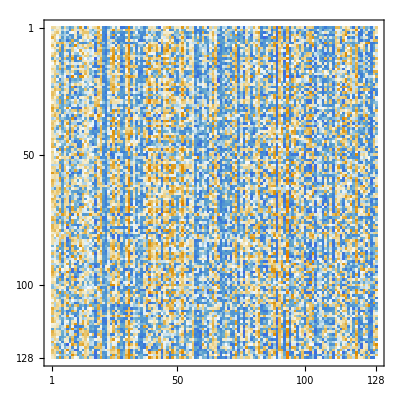

```mathematica
MatrixPlot[Take[logsFeaturesTest,UpTo[Length[First[logsFeaturesTest]]]]]
```

```mathematica
Detokenize[sequence0_List]:=Module[{sequence=sequence0,probabilities,text},(
probabilities=(ReplacePart[ConstantArray[0,tokensDimLM-1],#->1])&/@sequence;
text=StringJoin[detokenizer[probabilities]];

text
)]
```

```mathematica
Row[FeatureSpacePlot3D[#,Method->"TSNE",ImageSize->Medium]&/@{logsFeaturesTrain,logsFeaturesTest}]
```

-Graphics3D--Graphics3D-

```mathematica
{anomalyDetectionDatasetTrain,anomalyDetectionDatasetTest}=ResourceFunction["TrainTestSplit"][datasetTest];
Length/@{anomalyDetectionDatasetTrain,anomalyDetectionDatasetTest}
```

{160,40}

```mathematica
anomalyDetector=AnomalyDetection[ExtractFeatures/@Values[anomalyDetectionDatasetTrain],AcceptanceThreshold->0.00110415]
```

AnomalyDetectorFunction[…]

```mathematica
sample=Detokenize[Values[RandomChoice[anomalyDetectionDatasetTest]]]
```

081110 120410 35 INFO dfs.FSNamesystem: BLOCK* NameSystem.allocateBlock: /user/root/randtxt2/_temporary/_task_200811101024_0002_m_001080_0/part-01080. blk_2847401988110989655
081110 120429 29 INFO dfs.FSNamesystem: BLOCK* NameSystem.addStoredBlock: blockMap updated: 10.251.197.226:50010 is added to blk_4307207852226914003 size 67108864

```mathematica
sampleShuffled=StringRiffle[RandomSample[StringSplit[sample,"\n"]],"\n"]
```

081110 120429 29 INFO dfs.FSNamesystem: BLOCK* NameSystem.addStoredBlock: blockMap updated: 10.251.197.226:50010 is added to blk_4307207852226914003 size 67108864
081110 120410 35 INFO dfs.FSNamesystem: BLOCK* NameSystem.allocateBlock: /user/root/randtxt2/_temporary/_task_200811101024_0002_m_001080_0/part-01080. blk_2847401988110989655

```mathematica
anomalyDetector[ExtractFeatures[tokenizer[sample]],"RarerProbability"]
```

0.0107416

```mathematica
anomalyDetector[ExtractFeatures[tokenizer[sampleShuffled]],"RarerProbability"]
```

0.000194345

```mathematica
anomalyDetector[ExtractFeatures[tokenizer[sample]],"Decision"]
```

False

```mathematica
anomalyDetector[ExtractFeatures[tokenizer[sampleShuffled]],"Decision"]
```

True